# フーリェ解析

## Nav: top

## DNA塩基配列データの解析

テキスト解析のテクニックのひとつであるフーリェ解析をDNA塩基配列解析に適応します。

DNA塩基配列データはATGCの4文字からなるデータであることをうまく利用し、以下のように文字を数値に変換します。

A | 1
T | -1
G | ⅈ
C | -ⅈ

変換後、直接フーリエ解析を行うとピークを検出できます。
下図はphix174のゲノムDNA(5386塩基)に対して行った解析結果です。

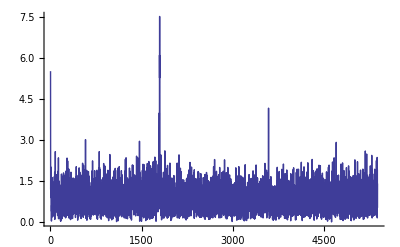

最も強度のある周波数は1798で、これに対応するシグナルの長さ、つまり配列の長さは2.997であり、コドンの長さ3と一致します。

高等生物のゲノムの特定の場所では、長さ3のシグナル以外に対しピークが出ることがあり、様々な発見に役立っています。

以上webコンテンツ

## めも

```mathematica
TableForm[Transpose[{{"A","T","G","C"},{1,-1,I,-I}}]]
```

A | 1
T | -1
G | ⅈ
C | -ⅈ

```mathematica
phix174genome=Import["ftp://ftp.ncbi.nlm.nih.gov/genomes/Viruses/Enterobacteria_phage_phiX174_sensu_lato_uid14015/NC_001422.fna"];
```

```mathematica
nucleotideToComplex[
  DNA_String] := (Characters[
     ToUpperCase[StringReplace[DNA, "\n" -> ""]]] /. {"A" -> 1, "T" -> -1, "G" -> I, "C" -> -I}) /. {_String -> 0};
```

```mathematica
(phix174genomeCpx=nucleotideToComplex[phix174genome[[1]]])//Length
```

5386

下記がスペクトルです。すこし注意して頂きたいことは、周波数nの強度は、n+1番目に示されることです。

```mathematica
ListPlot[Abs[Fourier[phix174genomeCpx]],Joined->True,PlotRange->All]
```

-Graphics-

最も強度のある周波数が以下です。

```mathematica
Position[Abs[Fourier[phix174genomeCpx]],Max[Abs[Fourier[phix174genomeCpx]]]]
```

{{1798}}

この周波数に対応するシグナルの長さは3で、これは、コドンの長さと一致します。

```mathematica
5386/(1798-1)//N
```

2.99722

## フーリェ解析

どのような分野でもそうですが、計量書誌学の世界でも他の分野からツールを借りて解析を行うことは多くあります。ひとつの例にフーリェ解析を文章構造の解析に用いることがあります。ここではさらに、それをバイオインフォマティクスに応用した例を紹介します。

```mathematica
phix174genome=Import["ftp://ftp.ncbi.nlm.nih.gov/genomes/Viruses/Enterobacteria_phage_phiX174_sensu_lato_uid14015/NC_001422.fna"];
```

```mathematica
nucleotideToComplex[
  DNA_String] := (Characters[
     ToUpperCase[StringReplace[DNA, "\n" -> ""]]] /. {"A" -> 1, "T" -> -1, "G" -> I, "C" -> -I}) /. {_String -> 0};
```

```mathematica
(phix174genomeCpx=nucleotideToComplex[phix174genome[[1]]])//Length
```

5386

下記がスペクトルです。すこし注意して頂きたいことは、周波数nの強度は、n+1番目に示されることです。

```mathematica
ListPlot[Abs[Fourier[phix174genomeCpx]],Joined->True,PlotRange->All]
```

-Graphics-

最も強度のある周波数が以下です。

```mathematica
Position[Abs[Fourier[phix174genomeCpx]],Max[Abs[Fourier[phix174genomeCpx]]]]
```

{{1798}}

この周波数に対応するシグナルの長さは3で、これは、コドンの長さと一致します。

```mathematica
5386/(1798-1)//N
```

2.99722